For Wolfram Summer Camp Students!

Contents

#### Introduction

#### Expressions

#### Patterns and rules

#### Pure functions

#### Using functions with Lists

#### Graphics

#### Basic vocabulary of functions

#### Real world entities

#### Other topics

## Introduction

Welcome! This notebook explains the basic know-how for using Mathematica. 

Helpful hints will appear in yellow, like this:

I am a helpful hint!

#### Further Preparation

I encourage you to do some combination of experimentation and further reading. Experimenting with Mathematica should be fun!

Wolfram Language documentation is available in the following forms:

The Fast Introduction for Programmers

The Elementary Introduction to the Wolfram Language

The Wolfram Language Documentation online

See the Overview page from the company's front page for a more complete description of Mathematica.

See the Notebook shortcuts page to learn about keyboard shortcuts.

#### Note!

At the end of almost every section, there are questions for you to answer.

## Expressions

Everything in the Wolfram Language is an expression.

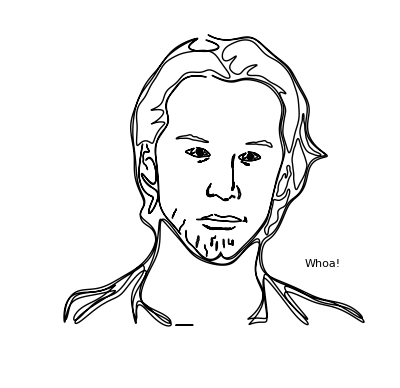

Mathematica expressions are like functions, with a function name and arguments, such as

```mathematica
Sin[1.5]
```

0.997495

With the cursor in the cell above, or with the cell highlighted, hit ⇧|⌤ to evaluate.

In every Wolfram Language expression, there is a Head, followed by a Sequence of arguments wrapped with square brackets. Function arguments can be numbers, symbols, or other Wolfram Language expressions. Built-in functions are capitalized.

In the example above, the Head is Sin and the argument is 1.5. There are many additional built-in functions like List or Table, but everything else is left to the user to define (or not define).

Head, Part and FullForm are built-in functions that help show the structure of an expression, e.g.,

```mathematica
Head[f[x,2,y]]
```

f

Uppercase and lowercase letters are recognized as different characters. Lists are wrapped with curly brackets.
{a, b, B}

To see the what argument is at a specific location in an expression, you can use Part.

For instance, to see the third element in a list {g[r],3,s[t],4}

```mathematica
Part[{g[r],3,s[t],4},3]
```

s[t]

Or you can use its shorthand notation:

```mathematica
{g[r],3,s[t],4}[[3]]
```

s[t]

Mathematica is made of two parts: a kernel and a front end. The kernel is the part that does calculations. The front end is the part that handles notebooks and interaction with the user.

The Mathematica front end sometimes disguises expressions so that they are not explicitly written in the form of a head and arguments enclosed in brackets. For instance it writes 2+z (Batman) instead of the full Mathematica expression Plus[2 ,z] (Bruce Wayne). And like Batman and Bruce Wayne, 2+z and Plus[2 ,z] are one and the same.

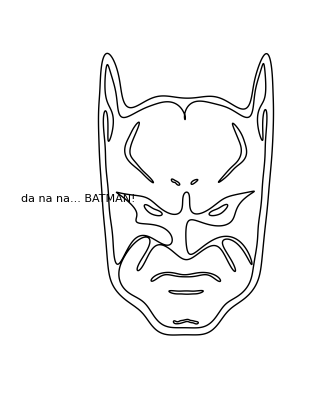

Each of these represents multiplication:
a*b 
a␣b 
a(b) 
Times[a, b]
2x means 2*x.

The function FullForm is used to display the full Mathematica form of an expression:

```mathematica
FullForm[2+z]
```

Plus[2,z]

```mathematica
FullForm[{2,3,s[t],4}]
```

List[2,3,s[t],4]

```mathematica
FullForm[x->1]
```

Rule[x,1]

```mathematica
FullForm[a==b]
```

Equal[a,b]

The following is explained in the Pure Functions section below

```mathematica
FullForm[#+1&]
```

Function[Plus[Slot[1],1]]

Expressions are automatically evaluated, whenever possible, but evaluation can be prevented using Hold. Among other things, you can use Hold to expose the Expression structure. Note that the following definition of the function g, contained within the braces of Hold, is a Mathematica expression.

```mathematica
FullForm[Hold[g[n]:=n^2]]
```

Hold[SetDelayed[g[n],Power[n,2]]]

There is a subtle difference between Set, "=", and SetDelayed, :=, but I won't go into it here, and instead refer you to this exposition in the Help Browser.

### Questions

1. What is the difference between the following two expressions?

Look in the documentation for Set and Equal. Try evaluating both in different orders - and use Clear in between. What is the value of x?

```mathematica
x==1
```

False

```mathematica
NSolve[x==1,{x}]
```

{{x→1.}}

```mathematica
x=1
```

1

The first one tests whether x is equal to 1 while the second assigns the variable x to the value of 1.

2. What happens when you evaluate the following expressions in different orders?

To test this properly, use Clear:
Clear[u,v]

```mathematica
u=v
```

v

```mathematica
u:=v
```

```mathematica
v=1
```

1

```mathematica
v:=0
```

Hint: you gotta check ‘em all!

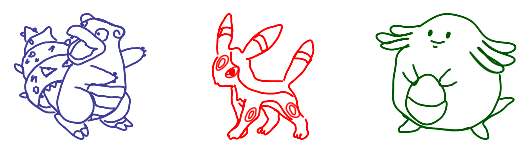

Since := is delayed assignment and = is immediate assignment, := is calculated after =. All assignments are calculated then delayed assignments are calculated.

## Patterns and rules

Suppose you have an expression and you want to change every 1 to a 2 and every 2 to a 1. The easiest way to do this is with a Rule application.

But what is a Rule? A Rule looks like this: a → b (or equivalently Rule[a, b]). It means: every time you see a,replace it with b.

For instance, here is a Graphics object.

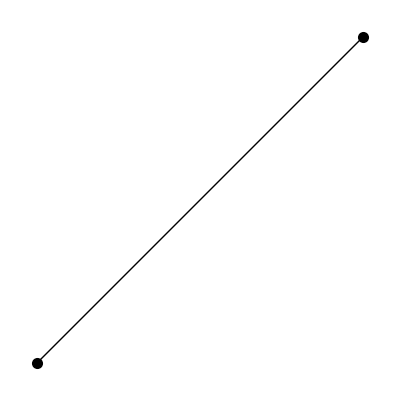

```mathematica
Graphics[{PointSize[.02],Point[{1,4}],Line[{{1,4},{2,5}}],Point[{2,5}]}]
```

Here is the same Graphics object after applying the List of Rules, {1->2, 2->1}, using /. (which is short for ReplaceAll). The result is that every occurrence of 1 in the expression becomes 2, and vice versa.

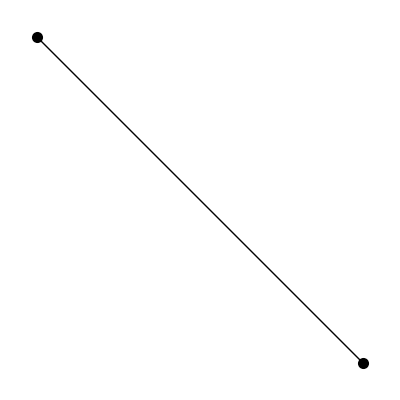

```mathematica
Graphics[{PointSize[.02],Point[{1,4}],Line[{{1,4},{2,5}}],Point[{2,5}]}]/.{1->2,2->1}
```

The left hand side of a rule can be any pattern. By pattern we mean any object or template against which other things will be compared to see if they match. For example, below we use the pattern _Integer which can be roughly translated in English as "any integer". The rule below turns every integer into the global variable a.

```mathematica
MatrixForm[{{1, 2, 3}, {4, 5, 6}, {7, 8, 9}}/._Integer->a]
```

(a | a | a
a | a | a
a | a | a)

Here is another example using the same replacement rule.

```mathematica
MatrixForm[IdentityMatrix[3]/._Integer->a]
```

(a | a | a
a | a | a
a | a | a)

Temporary variables can be used in a pattern. Here a_Integer means "any integer, temporarily stored in the temporary variable a".

This means that you could Set the global variable a to the value 5 (by doing a = 5), and it would not have any effect on the example below.

(4 | 1 | 1
1 | 4 | 1
1 | 1 | 4)

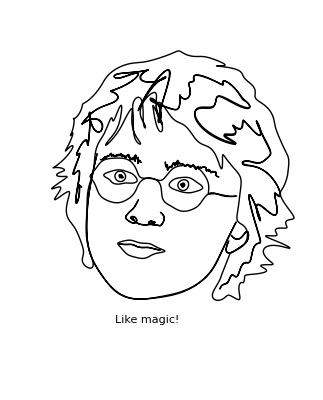

```mathematica
MatrixForm[IdentityMatrix[3]/.a_Integer:>(a+1)^2]
```

Patterns can be used in other ways like in the functions Count and Cases.

Here you count the number of zeros by using Count on the second level to match the pattern 0. 

A matrix is a list of lists; the terminology "first level" refers to those lists, while "second level" refers to the elements of those lists. The second level of the identity matrix is composed of 0's and 1's.

```mathematica
Count[IdentityMatrix[3],0,{2}]
```

6

```mathematica
Count[IdentityMatrix[3],1,{2}]
```

3

Here the pattern is any integer.

```mathematica
Count[IdentityMatrix[3],_Integer,{2}]
```

9

On the first level (the default of Count) of a matrix, there are only lists, no integers.

```mathematica
Count[IdentityMatrix[3],_Integer]
```

0

A pattern can just consist of the single _ or Blank[] which represents any single expression.

```mathematica
Count[IdentityMatrix[3],_]
```

3

```mathematica
Count[{g[r],2,s[t],4,s[5],S[3]},s[_]]
```

2

Below, Cases is used to find every case of a subexpression with the Head "s".

```mathematica
Cases[{g[r],2,s[t],4,s[5],S[3]},_s]
```

{s[t],s[5]}

If you are ever confused about levels, you can use the Mathematica function Level. In a new cell, try and compare the following:

Level[IdentityMatrix[3], {1}]
Level[IdentityMatrix[3], {2}]

### Questions

1. Unintended consequences are common in programming. What is going on in the following alteration of the previous Graphics example? Why are the colors different?

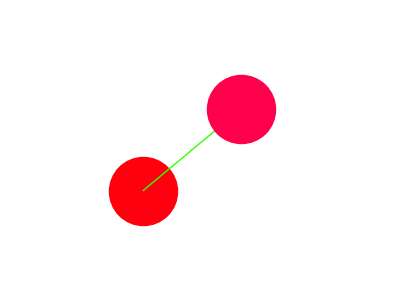

```mathematica
Graphics[{Hue[0.99],PointSize[.2],Point[{1,4}],Hue[.3],Line[{{1,4},{2,5}}],Hue[.95],Point[{2,5}]},PlotRange->{{-1,3},{3,6}}]/.{1->.3,2->1.5}
```

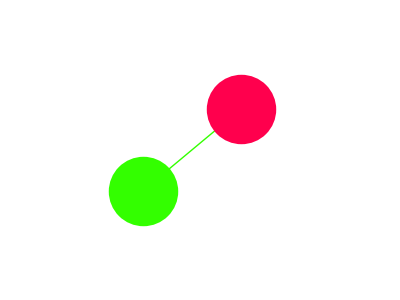

```mathematica
Graphics[{Hue[1],PointSize[.2],Point[{1,4}],Hue[.3],Line[{{1,4},{2,5}}],Hue[.95],Point[{2,5}]},PlotRange->{{-1,3},{3,6}}]/.{1->.3,2->1.5}
```

Due to the hue of the first circle being set to 1 in the second example, the first rule 1 -> 0.3 is being activated, setting it to 0.3, or green. In the first example, the hue of the first example is set to 0.99, so the rule does not activate.

2. In the following example, change every Point to a Circle with radius 1/2, centered around the point, using a Rule application.

(Try using Help to see how to use Circle, and remember to use a Rule application instead of re-typing the whole expression).

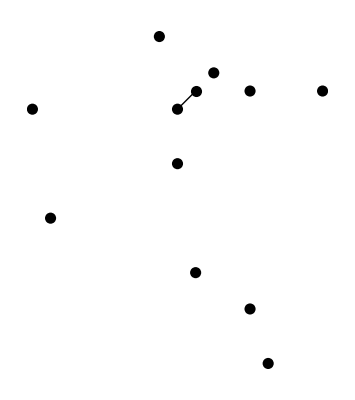

```mathematica
Graphics[{PointSize[.02],Point[{9,5}],Point[{2,-5}],Point[{5,5}],Point[{3,6}],Point[{1,1}],Point[{5,-7}],Point[{-7,4}],Point[{6,-10}],Point[{-6,-2}],Point[{0,8}],Point[{1,4}],Line[{{1,4},{2,5}}],Point[{2,5}]},AspectRatio->Automatic/.Point -> Circle[0.5]]
```

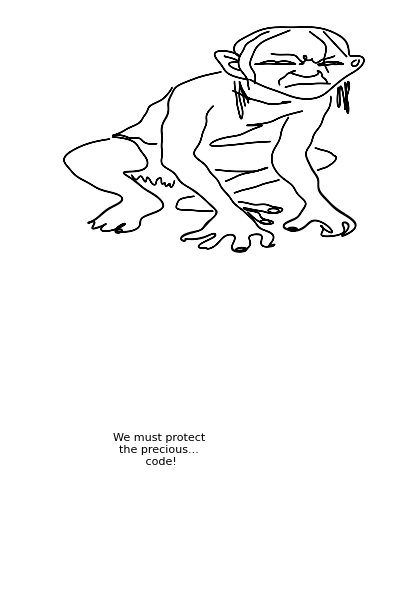

## Pure functions

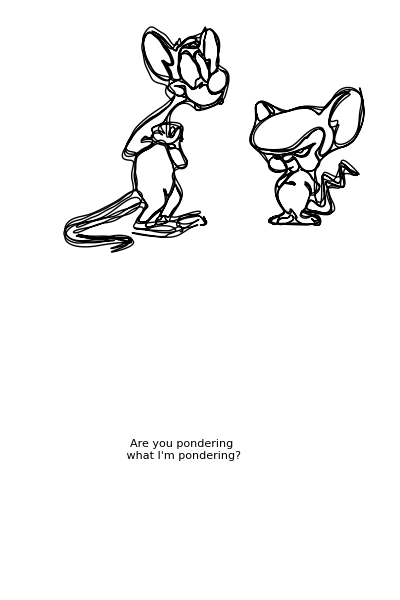

I don’t know! I am pondering how to define functions in Wolfram Language - are you?

One can define functions using pattern matching, e.g.,

```mathematica
g[n_Integer]:=n^2
```

```mathematica
g[5]
```

25

Alternatively, a pure function never gives a label to its arguments, and instead uses Slot, often displayed as #. For instance,

```mathematica
square=#^2&
```

#1^2&

By default # represents the first argument of a function, and can alternatively be written as #1.

```mathematica
FullForm[square]
```

Function[Power[Slot[1],2]]

Note the importance of the &, which is needed to make it a function:

```mathematica
FullForm[#^2]
```

Power[Slot[1],2]

Pure functions can be applied like any other function.

```mathematica
square[3]
```

9

Total[{##1}]&

6

```mathematica
g[3]
```

9

A pure function can take any number of arguments. What is it doing with the second argument in this case?

```mathematica
square[3]
```

9

What is g doing in this case?

```mathematica
g[3,4]
```

g[3,4]

Here’s another example, with three arguments.

```mathematica
superpower=#1^(#2^#3)&
```

#1^(#2^#3)&

And in FullForm...

```mathematica
FullForm[superpower]
```

Function[Power[Slot[1],Power[Slot[2],Slot[3]]]]

```mathematica
superpower[2,3,4]
```

2417851639229258349412352

```mathematica
3^4
```

81

```mathematica
2^%
```

2417851639229258349412352

The % symbol is used to represent the most recent output. This can come in quite handy!

Note that a pure function does not need to be set as a symbol, e.g.,

83

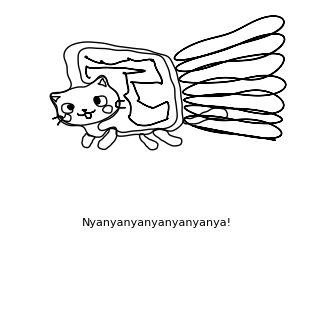

```mathematica
(#+#2^#3&)[2,3,4]
```

### Questions

1. Write a pure function to add together any number of arguments.

```mathematica
Total[List[##]]&
```

2. Now, write a (not pure) function to add together any number of arguments.

```mathematica
sum[x__]:=Total[List[x]]
s[1, True, 3]
```

s[1,True,3]

3. Challenge! Write a function that adds together any number of integers, and does not evaluate if any noninteger arguments are present.

```mathematica
s[x__Integer] := Total[List[x]]
```

## Using functions with Lists

There are several situations where one wants to use a function on every element in a list.

Suppose you have a list, and you want to apply a function to every element in that list separately. The right way to do this is to use the function Map.

```mathematica
Map[f,{a,b,c,d}]
```

{f[a],f[b],f[c],f[d]}

Say you have a random matrix of 0's and 1's, and you want to take the Total of each row.

```mathematica
randombits=RandomInteger[{0,1},{5,5}]
```

{{1,1,0,1,0},{0,0,0,0,1},{1,0,0,1,1},{1,1,1,0,0},{1,1,0,0,0}}

```mathematica
randombits//MatrixForm
```

(1 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

To do this, use Map, or equivalently the short cut /@, with Total as follows:

Map[function, list] is the same as function /@ list.

```mathematica
Total/@randombits
```

{3,1,3,3,2}

Now take a matrix of digits, and say you want to know which digits occur. The function to use is Union.

```mathematica
randomdigits=RandomInteger[{0,9},{3,3}]
```

{{0,1,3},{2,4,9},{6,5,7}}

```mathematica
randomdigits//MatrixForm
```

(0 | 1 | 3
2 | 4 | 9
6 | 5 | 7)

but if you try Union, it doesn't do what you wanted because you asked it to take a union of a single list of three lists. The three lists are considered basic units.

```mathematica
Union[randomdigits]
```

Part::partd: Part specification randomdigits⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression randomdigits cannot be used as a part specification.

1⟦randomdigits⟧

Instead, you want to take a union of the three lists. One approach is to use the function Apply. It replaces the head of the expression with Union.

Apply[function, List[arguments]] returns function[arguments].

```mathematica
Apply[Union, randomdigits]
```

{0,1,2,3,4,5,6,7,9}

```mathematica
Apply[f, randomdigits]
```

f[{0,1,3},{2,4,9},{6,5,7}]

As with Map, the function Apply also has a shortcut, @@

function @@ argument is equivalent to Apply[function, argument].

{0,1,2,3,4,5,6,7,9}

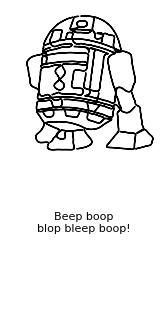

```mathematica
Union@@randomdigits
```

### Questions

1. Use Map and Count to find the number of 1's in each row of a random 10 x 10 matrix whose entries are all 0s and 1s.

Hint: you might want to use a pure function with Count.

```mathematica
Map[Count[##, 1]&,RandomInteger[{0, 1}, {10, 10}]]
```

{5,5,1,5,7,6,5,7,5,5}

2. Use Apply and SameQ to determine if all of the arguments of the expression below are the same. In what instance might they be the same even though they appear different?

```mathematica
Apply[SameQ,f[a, b,a,d]]
```

False

3. A one-dimensional cellular automaton consists of two things: a row of cells and a set of rules. Each cell can be in one of a number of states, and the rules determine how these cells interact with their neighbors over time. You can model these with Mathematica.

The following shows how three cells evolve in one time step with a set of rules (under Rule 90). The first list shows the cells initially, and the second list shows how the cells evolve under the rules.

```mathematica
CellularAutomaton[90, {{1}, 0}, 1]
```

{{0,1,0},{1,0,1}}

You can better visualize this with ArrayPlot. As before, the first row is the initial state of the cells, and the second is the evolved cells.

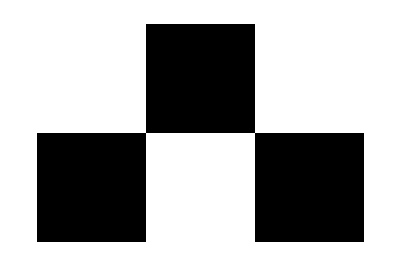

```mathematica
ArrayPlot[CellularAutomaton[90, {{1}, 0}, 1]]
```

For fun, see what happens after 2^10 time steps. Do you recognize this image?

ArrayPlot[CellularAutomaton[90, {{1}, 0}, 2^10]]

4. Use Map and Total to find the sum of each row of the Cellular Automaton in the following evolution.

```mathematica
Map[Total,CellularAutomaton[90,{{1},0},2^6]]
```

```mathematica
Map[Count[##, 1]&,CellularAutomaton[90,{{1},0},2^6]]
```

{1,2,2,4,2,4,4,8,2,4,4,8,4,8,8,16,2,4,4,8,4,8,8,16,4,8,8,16,8,16,16,32,2,4,4,8,4,8,8,16,4,8,8,16,8,16,16,32,4,8,8,16,8,16,16,32,8,16,16,32,16,32,32,64,2}

{1,2,2,4,2,4,4,8,2,4,4,8,4,8,8,16,2,4,4,8,4,8,8,16,4,8,8,16,8,16,16,32,2,4,4,8,4,8,8,16,4,8,8,16,8,16,16,32,4,8,8,16,8,16,16,32,8,16,16,32,16,32,32,64,2}

5. Now, use Map and Count to find the number of “1”s on each row of the Cellular Automaton in the following list of evolutions.

## Graphics

Graphics are important for math, research, science, art, fun, analysis, and just about everything! Again, you should experiment with the various possibilities found in the examples in the Help browser. I will give a couple of examples here (but you have already seen some in this notebook!).

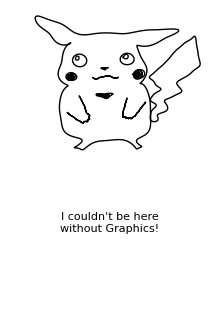

Graphics is for 2 dimensional graphics, and in the case of a one dimensional evolution, ArrayPlot is a convenient way to display a matrix, or a list of lists.

Here CellularAutomaton produces a matrix of 0's and 1's where s row shows what the automaton looks like at that step in time.

```mathematica
ArrayPlot[CellularAutomaton[90,{{1},0},2^5-1]]
```

-Graphics-

You can do this for any matrix.

```mathematica
ArrayPlot[RandomInteger[10,{20, 20}]]
```

-Graphics-

And you can add color!

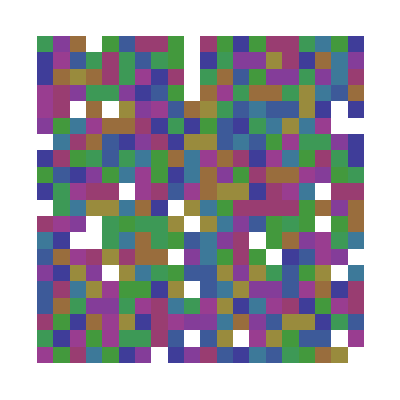

```mathematica
ArrayPlot[RandomInteger[10,{20, 20}], ColorRules->(# :> ColorData[1][#] & /@ Range[10])]
```

Graphics can do much more than just plot matrices. There is a list of available primitives in the help browser.

```mathematica
Graphics[{
		Lighter @ Yellow, 
			Disk[], 
		Black, 
			Disk[.5{Cos[Pi/4], Sin[Pi/4]}, .1], 
			Disk[.5{-Cos[Pi/4], Sin[Pi/4]}, .1],
			Disk[{0, 0}, .05],
		Thick, Red,
			BezierCurve[{{-.5, -.2}, {0, -1.2}, {.5, -.2}}],
			Line[{{-.5, -.2}, {.5, -.2}}]
		}]
```

Graphics3D is for 3-dimensional graphics. There is a list of available primitives in the help browser, as is the case also for Graphics used above.

The following displays 35 cubes placed randomly on the integer lattice in 3 dimensions (with each component in the range of -10 and 10).

```mathematica
Graphics3D[Cuboid/@Union[Table[RandomInteger[{-10,10}],{35},{3}]]]
```

Here they are placed randomly according to a distribution derived from polar coordinates.

```mathematica
Graphics3D[Cuboid/@Table[3Tan[RandomReal[{-Pi/2,Pi/2}]],{35},{3}]]
```

And here is a colorful example from the documentation:

```mathematica
Graphics3D[Table[With[{p={i,j,k}/5},{RGBColor[p],Opacity[.75],Cuboid[p,p+.15]}],{i,5},{j,5},{k,5}]]
```

#### Questions

1. What is going on in the following graphic?

```mathematica
Graphics3D[{Line/@Partition[#,2,1,1],Cuboid/@#}]&[Union[Table[RandomInteger[{-10,10}],{15},{3}]],PlotRange->All]
```

-Graphics3D-

A bunch of randomly placed small cubes are inside a larger transparent cube.

```mathematica
Graphics3D[{Line/@Partition[#,3,1,1],Sphere/@#}]&[Union[Table[RandomInteger[{-10,10}],{15},{3}]],PlotRange->All]
```

-Graphics3D-

2. Make your own graphics! One using Graphics and one using Graphics3D. We will display and discuss these with the class, so have fun with this!

## Basic vocabulary of functions

There are many candidates for basic functions everyone should know.  You have seen here some of my favorites:  Equal, Part, List, SetDelayed, ReplaceAll, Pattern, Blank, Rule, Slot, Function. Note that each of these functions has a short form representation used in InputForm, StandardForm, etc. Recall =, {}, :=, /., _, #, &, etc.

After learning those, another collection of important functions are Table, Array, Map, Apply, NestList, Fold, and their friends. Explore these using the documentation.

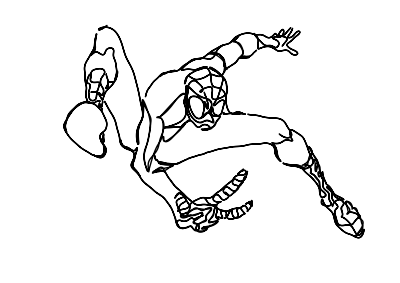

#### Questions

1. Write a short piece of code which sums the first n primes, using the built-in functions Array, Fold, Plus and Prime.

```mathematica
f[n_] := Fold[Plus, 0, Array[Prime[#]&, n]]
```

639

2. Make the same function using the built-in functions Apply, Plus, Prime and Table.

```mathematica
f[n_] := Apply[Plus, Table[Prime[i], {i, n}]]
```

2

5

3. Do it again, using just Prime and Sum.

```mathematica
f[n_] := Sum[Prime[i], {i, n}]
```

2

5

## Real world entities

The Wolfram Language has built in syntax for representing real world objects and concepts, and properties about them.

To access these object, you can use natural language to ask for them! Use the command  to pop open a natural language input box and type your query.

```mathematica
LinguisticAssistant
```

Press return (enter) to evaluate.

```mathematica
LinguisticAssistant
```

What are properties of the Apollo 11 mission we can ask about?

```mathematica
EntityProperties[Entity["MannedSpaceMission","Apollo11"]]
```

{alternate names,callsign,command and service module callsign,operator countries,crew,description,disciplines,distance traveled,Earth landing date,funding agencies,image,lunar landing location,launch date,launch site,launch vehicle,lunar landing date,lunar module callsign,mass,maximum altitude,maximum velocity,mission duration,name,NORAD number,international designator,orbiter,peak acceleration,position,primary crew,moonwalk date}

Here’s the crew and an image.

```mathematica
EntityValue[Entity["MannedSpaceMission","Apollo11"],{EntityProperty["MannedSpaceMission","Crew"],EntityProperty["MannedSpaceMission","Image"]}]
```

{{Neil Armstrong,Michael Collins,Buzz Aldrin},-Graphics-}

Using  let’s ask for “the 20 tallest buildings in the world” and plot their locations on a map.

```mathematica
GeoListPlot[LinguisticAssistant,GeoRange->"World"]
```

-Graphics-

#### Questions

1. Run the command EnityValue[] to see all types of entities available in Wolfram Language.

```mathematica
EntityValue[]
```

{AdministrativeDivision,Aircraft,Airline,Airport,Alphabet,AmusementPark,AmusementParkRide,AnatomicalFunctionalConcept,AnatomicalStructure,Artwork,AstronomicalObservatory,AstronomicalRadioSource,AtmosphericLayer,BasicFoodGroup,Beach,BoardGame,Book,Bridge,BroadcastStation,BroadcastStationClassification,Building,Canal,Castle,CatBreed,Cave,Cemetery,Character,Chemical,City,Cloud,CognitiveTask,Color,Comet,Company,ComputationalComplexityClass,Concept,Constellation,ContinuedFraction,ContinuedFractionResult,ContinuedFractionSource,Country,CrystalFamily,CrystallographicSpaceGroup,CrystalSystem,CurrencyDenomination,Dam,DeepSpaceProbe,Desert,Digimon,Dinosaur,Disease,DisplayFormat,DistrictCourt,DogBreed,EarthImpact,Earthquake,Element,Exoplanet,FamousChemistryProblem,FamousGem,FamousMathGame,FamousMathProblem,FamousPhysicsProblem,FictionalCharacter,FileFormat,Financial,FiniteGroup,Food,FoodAge,FoodAlcoholLabel,FoodBeefGrade,FoodBoneContent,FoodBrandName,FoodCaffeineLabel,FoodCalorieLabel,FoodComposition,FoodConcentration,FoodCrustType,FoodCulture,FoodDataSource,FoodFatLabel,FoodFatType,FoodFiberLabel,FoodFlavor,FoodGeometryType,FoodIntendedUse,FoodIronLabel,FoodLocation,FoodManufacturer,FoodMeatCut,FoodMeatQuality,FoodMoistureLevel,FoodNutritionalSupplement,FoodNutritionalSupplementNotAdded,FoodPackaging,FoodPart,FoodPattyCount,FoodPeelingType,FoodPreparation,FoodProcessingType,FoodSeafoodVariety,FoodSeedContent,FoodServingType,FoodSize,FoodSkinContent,FoodSodiumLabel,FoodState,FoodStorageType,FoodSubBrandName,FoodSugarLabel,FoodSugarType,FoodTexture,FoodTrimmingLevel,FoodType,FoodTypeGroup,FoodVariety,FoodVegetablePart,Forest,FrequencyAllocation,FunctionalAnalysisSource,FunctionSpace,Galaxy,Gene,GeographicRegion,GeologicalLayer,GeologicalPeriod,GivenName,Glacier,GrammaticalUnit,Graph,HistoricalCountry,HistoricalEvent,HistoricalPeriod,HistoricalSite,ICDNine,ICDTen,Icon,IntegerSequence,InternetDomain,IPAddress,Island,ISO15924Group,Isotope,Knot,Lake,Lamina,Language,Lattice,LatticeSystem,LibraryBranch,LibrarySystem,MannedSpaceMission,MathematicalFunction,MathWorld,MeasurementDevice,MedicalTest,MeteorShower,MetropolitanArea,Mine,Mineral,MinorPlanet,Mountain,Movie,Museum,MusicAct,MusicAlbum,MusicAlbumRelease,MusicalInstrument,MusicWork,MusicWorkRecording,Mythology,Nebula,Neighborhood,NetworkService,Neuron,NonperiodicTiling,NotableComputer,NuclearExplosion,NuclearReactor,NuclearTestSite,Ocean,OilField,Park,Particle,ParticleAccelerator,Periodical,PeriodicTiling,Person,PersonTitle,PhysicalSystem,PilatesExercise,PlaneCurve,Planet,PlanetaryMoon,Plant,Pokemon,Polyhedron,PopularCurve,PreservationStatus,PrivateSchool,ProgrammingLanguage,Protein,PublicSchool,Pulsar,Reef,Religion,ReserveLand,RiemannHypothesisFormulation,River,Rocket,Satellite,SchoolDistrict,Ship,Shipwreck,SNP,SolarSystemFeature,Solid,Source,SpaceCurve,Species,SportMatch,SportObject,Stadium,Star,StarCluster,Supernova,Surface,Surname,TimeZone,TopLevelDomain,TopologicalSpaceType,TropicalStorm,Tunnel,UnderseaFeature,University,USCongressionalDistrict,USDAFoodGroup,Volcano,Waterfall,WeatherStation,WolframLanguageSymbol,Word,WritingDirection,WritingScript,WritingScriptBaseline,WritingScriptType,YogaPose,YogaPosition,YogaProp,YogaSequence,ZIPCode}

2. Use  to find the capital city of France.

```mathematica
LinguisticAssistant
```

Paris

3. Use the Wolfram Language to determine which Pokémon Pikachu evolves into.

```mathematica
LinguisticAssistant
```

{Raichu}

## Other topics

Other topics worth checking into are Level specifications, List manipulations like Partition and Flatten, Outer, Clear, Condition (/;), Position, Select, Union, Complement, MatchQ, RuleDelayed, and, to a lesser extent, String manipulation and attributes.

Go explore! We look forward to learning Wolfram Language with you.